# Fitting the binding curve

## Reading the data

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[], "2023.02.21.13.19.23"}]];
```

```mathematica
distances=BinaryReadList["distances.dat","Real32"];
angles=BinaryReadList["angles.dat","Real32"];
bindingEnergies=ArrayReshape[BinaryReadList["binding_energies.dat","Real32"],{Length[angles], Length[distances]}];
```

## Morse potential

```mathematica
angleIDX=8;
startingDistance=11;
scatter=Table[{distances[[i]],bindingEnergies[[angleIDX,i]]},{i,startingDistance,Length[distances]-startingDistance}];
```

```mathematica
nlm=Normal[NonlinearModelFit[scatter,De(Exp[-2a(r-re)]-2Exp[-a(r-re)]),{De,a,re},r]]
```

0.461625 (ⅇ^(-5.47374 (-0.538269+r))-2 ⅇ^(-2.73687 (-0.538269+r)))

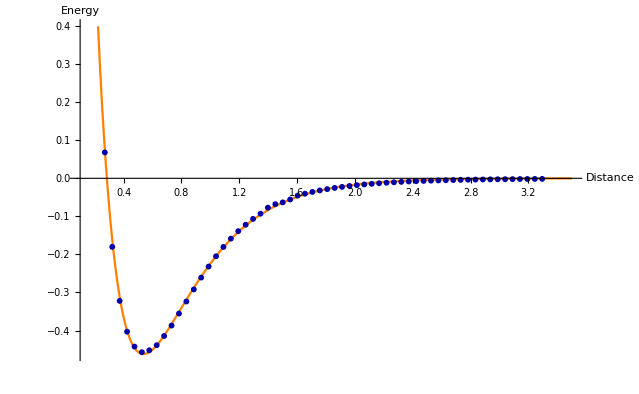

```mathematica
Clear[f]
f[r_]:=0.46162512831719266 (ⅇ^(-5.473740049665798 (-0.5382686719819294+r))-2 ⅇ^(-2.736870024832899 (-0.5382686719819294+r)))
Show[Plot[f[x],{x,0.1,3.5},PlotStyle->{Orange},AxesLabel ->{Distance,Energy}],ListPlot[scatter[[;; ;; 3]],PlotMarkers->{Automatic,6},PlotStyle->Darker[Blue]]]
```

```mathematica
★ ● ▲ ■
```

```mathematica
FortranForm[0.46162512831719266 (ⅇ^(-5.473740049665798 (-0.5382686719819294+r))-2 ⅇ^(-2.736870024832899 (-0.5382686719819294+r)))]
```

0.46162512831719266*(E**(-5.473740049665798*(-0.5382686719819294 + r)) - 
     -    2/E**(2.736870024832899*(-0.5382686719819294 + r)))

## Lennard-Jonnes (doesn’t work so well)

```mathematica
Clear[ϵ,σ]
nlm=Normal[NonlinearModelFit[scatter,4ϵ((σ/r)^12-(σ/r)^6),{ϵ,σ},r]]
```

0.398034 (0.0000290955/r^12-0.00539402/r^6)

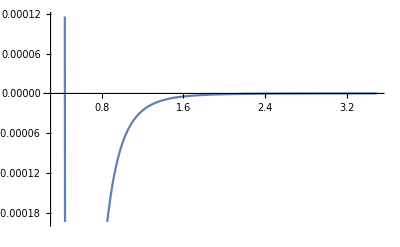

```mathematica
Clear[f]
f[r_]:=0.010619523843508963 (0.000053110959268918895/r^12-0.007287726618700713/r^6)
Show[Plot[f[r],{r,0.3,3.5}],ListPlot[scatter]]
```